## 3.029 Spring 2022 Lecture 13 - 03/14/2022

## Molecular Dynamics

In the last couple of lectures, we investigated polymer dynamics using a closed form viscous-dragging motion for reptation

Today, we will end our unit on classical dynamics, by investigating a numerical technique for modeling the dynamics of atoms and molecules more generally

In doing so, we will quickly re-visit Hamiltonian and Newtonian mechanics from L01-L03

## Symplectic Integration

Recall that instead of solving for N 2^nd order differential equations using Newton’s second law of motion

We can instead solve the 2N 1^st order Hamilton’s equations given by

In L01-L02, we saw how this often leads to a simplified description for complex systems

Here, we will make use of another property of Hamilton’s equations

Namely, that the Geometry of Hamiltonian Systems enables energy-conserving integration schemes, which are numerically more stable

### Lennard Jones Potential

Recall that the normalized Lennard-Jones potential is given by

For two particles a normalized distance  apart

```mathematica
lennardJonesPotentialNonDimensional[ρ_]=1/ρ^12-2/ρ^6;
```

The magnitude of the force experienced by the particles is given by

```mathematica
lennardJonesForce[ρ_]=-lennardJonesPotentialNonDimensional'[ρ]
```

12/ρ^13-12/ρ^7

To obtain the force vector we need to specify the generalized coordinates and take the vector-calculus gradient (Grad) instead

In 2D, we can specify the positions using ((x_A,y_A),(x_B,y_B))

```mathematica
Block[{
posA={xA,yA},posB={xB,yB},
vectorConnectingAB,
distanceAB,
ljp
},

vectorConnectingAB=posA-posB;
distanceAB=√(vectorConnectingAB.vectorConnectingAB);
ljp=lennardJonesPotentialNonDimensional[distanceAB];

Grad[-ljp,posA]
]
```

{(12 (xA-xB))/(((xA-xB)^2+(yA-yB)^2)^7)-(12 (xA-xB))/(((xA-xB)^2+(yA-yB)^2)^4),(12 (yA-yB))/(((xA-xB)^2+(yA-yB)^2)^7)-(12 (yA-yB))/(((xA-xB)^2+(yA-yB)^2)^4)}

This can be equivalently written as

Note: The Lennard-Jones potential is a pair-potential, meaning we have to compute these for all pairs of particles

Naively, this relies on computing pairwise distances and has a N^2 complexity

We discussed how to do this (somewhat) efficiently last lecture using DistanceMatrix

```mathematica
With[{pts=RandomReal[{-1,1},{3,2}]},
MatrixForm[DistanceMatrix[pts]]
]
```

(0. | 0.557963 | 1.64892
0.557963 | 0. | 1.98949
1.64892 | 1.98949 | 0.)

Note however that the diagonal distance (naturally) returns zero which will blow up our force calculation.
Since we don’t want to compute forces for self-interactions, we will set this to the equilibrium distance of 1 (no-force)

```mathematica
With[{pts=RandomReal[{-1,1},{3,2}]},
MatrixForm[DistanceMatrix[pts]+IdentityMatrix[Length[pts]]]
]
```

(1. | 1.0198 | 0.205566
1.0198 | 1. | 1.0597
0.205566 | 1.0597 | 1.)

We can write a function to compute all the forces given a list of particles

By summing over the columns of the DistanceMatrix

```mathematica
lennardJonesForces[pts_?MatrixQ]:= Block[
{differenceMat = Outer[Subtract,pts,pts,1],
distanceMatSquared =DistanceMatrix[pts, DistanceFunction->SquaredEuclideanDistance] + IdentityMatrix[Length[pts]],
distanceMatSixth,forceMatrix
},
distanceMatSixth= distanceMatSquared^3;
Total[((-12 differenceMat) ( 1-distanceMatSixth))/distanceMatSquared^7]
]
```

```mathematica
With[{pts=RandomReal[{-1,1},{3,2}]},
lennardJonesForces[pts]
]
```

{{-0.564555,0.853479},{19685.8,-68027.2},{-19685.3,68026.3}}

We’ll start by simulating a square grid of particles

```mathematica
With[{pts=Tuples[Range[-5,5],2]},
Graphics[Disk[#,3/8]&/@pts]
]
```

In-fact, let’s write a simple visualization function to color these with their total LennardJones Potential

First, we need a function to compute the total Energies

```mathematica
lennardJonesEnergies[pts_?MatrixQ]:= Block[
{
distanceMatSquared =DistanceMatrix[pts, DistanceFunction->SquaredEuclideanDistance] + IdentityMatrix[Length[pts]],
distanceMatSixth
},
distanceMatSixth= distanceMatSquared^3;
Total[1/distanceMatSixth - 2/distanceMatSixth^2]
]
```

Then, we rescale the colors to a global min/max range

```mathematica
cf=With[{cols={Darker[XYZColor[1,0.2,1]],LUVColor[.16,.5,1]}},
ResourceFunction["DivergentColorFunction"][cols]];
colorFunction=cf[3/2+#/4]& ;

particleGraphic[pts_?MatrixQ]:= Graphics[
MapThread[{colorFunction[#2],Disk[#1,3/8]}&,{pts,lennardJonesEnergies[pts]}]
]
```

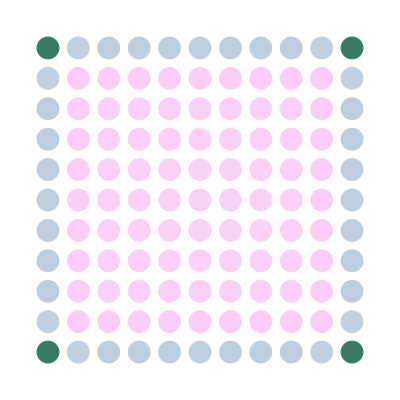

```mathematica
particleGraphic[N[Tuples[Range[-5,5],2]]]
```

We are now ready to solve Hamilton’s equations directly using `NDSolveValue`

```mathematica
{ljSquareLatticePositions,ljSquareLatticeMomenta} =With[{initialPositions=N[Tuples[Range[-5,5],2]],initialMomenta=ConstantArray[0.,{(2 5+1)^2,2}]},
NDSolveValue[{
p'[t]==lennardJonesForces[q[t]],
q'[t] == p[t], 

p[0] == initialMomenta,
q[0]== initialPositions
},{q,p},{t,0,20},

Method->{"SymplecticPartitionedRungeKutta","DifferenceOrder"->2,"PositionVariables"->{q[t]}},

StartingStepSize->1/50,MaxSteps->Infinity]
];
```

The solution exhibits a mechanical instability

highlighting that the square lattice is not stable for a 2D material

quickly changing to a hexagonal lattice instead

```mathematica
Manipulate[
Show[
particleGraphic[ljSquareLatticePositions[t]],
PlotRange-> 7{{-1,1},{-1,1}}],
{{t,0,"Time"},0,20},Paneled->False
]
```

## Velocity Verlet Integration

The Symplectic Integration scheme above is elegant and (fairly) fast

Importantly, since it conserves total energy - some of the potential energy from the LJ interaction is transferred to kinetic energy

Our system is adiabatic, and thus we can relate the increased kinetic energy with a “temperature”

If we wanted to “cool” the system down - we could add a damping factor to the particles’ velocities

To do this - we will develop a general integration scheme based on solving Newton’s equations instead

### Integration Schemes

Remember, in Newtonian mechanics methods, we wish to solve, for all particles, the equation

To do this numerically, we introduce a discretization of time using a Taylor series

```mathematica
Series[x[t],{t,t0,2}]
```

x[t0]+x'[t0] (t-t0)+1/2 x''[t0] (t-t0)^2+O[t-t0]^3

Defining our time-step , we obtain the Euler Scheme

This turns out to not be very numerically-stable

Let’s look at a simple 1D example - the harmonic oscillator

```mathematica
simpleHarmonicOscillatorEulersMethod[{k_,m_},Δt_:0.01][{position_,velocity_}]:=Block[{force=- k position/m,velocityNew,positionNew},
positionNew=position + velocity Δt (*+1/2force Δt^2*);
velocityNew=velocity  +force Δt;
{positionNew,velocityNew}
]
```

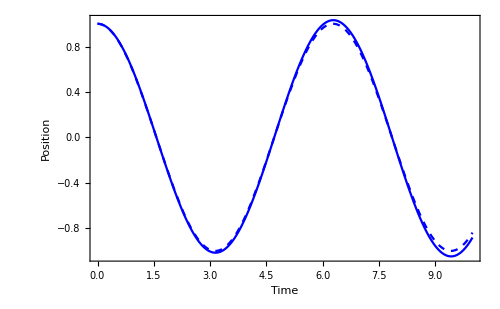

```mathematica
With[{
positions=NestList[simpleHarmonicOscillatorEulersMethod[{1,1}],{1,0},1000][[All,1]],
times=Range[0,1000]0.01},
Show[
ListLinePlot[Thread[{times,positions}],Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->Blue,BaseStyle->18,ImageSize->500,FrameLabel->{"Time","Position"}],
Plot[Cos[t],{t,0,10},PlotStyle->Directive[Blue,Dashed]]
]
]
```

The solution quickly diverges from the true solution (dashed)

The Verlet integration schemes achieves better accuracy

by taking a Taylor expansion in the forward and backwards direction

Summing the two together we obtain

```mathematica
simpleHarmonicOscillatorVerletMethod[{k_,m_},Δt_:0.01][{position_,previousPosition_}]:=Block[{force=- k position/m,positionNew},
positionNew=2position -previousPosition +force Δt^2;
{positionNew,position}
]
```

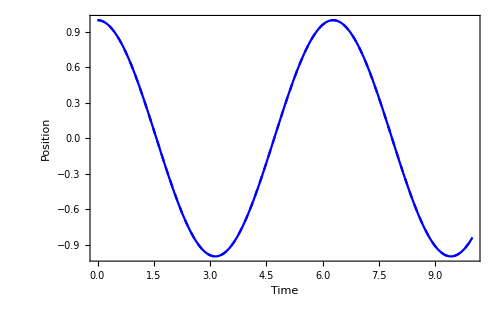

```mathematica
With[{
positions=Prepend[NestList[simpleHarmonicOscillatorVerletMethod[{1,1}],{0.99995,1},999][[All,1]],1],
times=Range[0,1000]0.01},
Show[
ListLinePlot[Thread[{times,positions}],Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->Blue,BaseStyle->18,ImageSize->500,FrameLabel->{"Time","Position"}],
Plot[Cos[t],{t,0,10},PlotStyle->Directive[Blue,Dashed]]
]
]
```

The solution is visibly much better!

Let’s plot the relative error of the solution instead

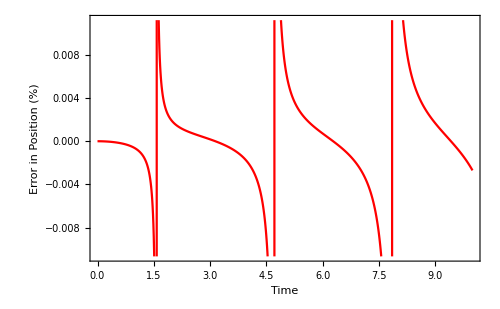

```mathematica
With[{
positions=Prepend[NestList[simpleHarmonicOscillatorVerletMethod[{1,1}],{0.99995,1},999][[All,1]],1],
truePositions=Cos/@Subdivide[0,10,1000],
times=Range[0,1000]0.01},
ListLinePlot[Thread[{times,(positions-truePositions)/truePositions 100}],Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->Red,BaseStyle->18,ImageSize->500,FrameLabel->{"Time","Error in Position (%)"}]
]
```

Note that the algorithm is not “self-starting” however

I.e. we required knowledge of

And also we don’t have direct access to high-accuracy velocities

which was our goal, to be able to adjust temperature

This brings us to the velocity-Verlet algorithm

This is more simply given by considering intermediate “half-steps”

Step 1: Calculate new position

Step 2: Calculate intermediate velocity

Step 3: Calculate new acceleration,  using

Step 4: Calculate new velocity

```mathematica
simpleHarmonicOscillatorVelocityVerletMethod[{k_,m_},Δt_:0.01][{position_,velocity_}]:=Block[{force=- k position/m,positionNew,velocityIntermediate,forceNew},
positionNew=position +velocity Δt +force Δt^2/2;
velocityIntermediate=velocity+force Δt/2;
forceNew=-k positionNew/m;
{positionNew,velocityIntermediate+forceNew Δt/2}
]
```

```mathematica
With[{
positions=NestList[simpleHarmonicOscillatorVelocityVerletMethod[{1,1}],{1,0},1000][[All,1]],
times=Range[0,1000]0.01},
Show[
ListLinePlot[Thread[{times,positions}],Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->Blue,BaseStyle->18,ImageSize->500,FrameLabel->{"Time","Position"}],
Plot[Cos[t],{t,0,10},PlotStyle->Directive[Blue,Dashed]]
]
]
```

-Graphics-

### Damped Evolution

We now have an accurate self-starting integrator for both positions and velocities

This means we can also add a damping factor to our velocities, to simulate a cooling down in temperature

```mathematica
velocityVerletDamping[dt_,dampingFactor_:1,computeForcesFunction_:lennardJonesForces][{positions_,velocities_,forces_}]:=Block[{newPositions,newVelocities,newForces},
newPositions=positions+velocities dt + 0.5 forces dt^2;
newForces = computeForcesFunction[newPositions];
newVelocities= dampingFactor(velocities + (forces+newForces)dt/2);
{newPositions,newVelocities,newForces}
]
```

We’ll start with the last frame of our previous simulation and cool the system down by introducing a slow velocity damping

```mathematica
positionsSquareLattice=ljSquareLatticePositions[20];
velocitiesSquareLattice=ConstantArray[0.,Dimensions[positionsSquareLattice]];
forcesSquareLattice=lennardJonesForces[positionsSquareLattice];
```

```mathematica
Dynamic[particleGraphic[positionsSquareLattice]]
```

```mathematica
Do[
{positionsSquareLattice,velocitiesSquareLattice,forcesSquareLattice}=velocityVerletDamping[0.01,0.99][{positionsSquareLattice,velocitiesSquareLattice,forcesSquareLattice}],
{1000}]
```

$Aborted

We can now use these “damped” positions - which should be closer to relaxed equilibrium positions

as initial conditions to our energy-conserving adiabatic solver

```mathematica
{ljSquareLatticePositionsRelaxed,ljSquareLatticeMomentaRelaxed} =With[{initialPositions=positionsSquareLattice,initialMomenta=ConstantArray[0.,{(2 5+1)^2,2}]},
NDSolveValue[{
p'[t]==lennardJonesForces[q[t]],
q'[t] == p[t], 

p[0] == initialMomenta,
q[0]== initialPositions
},{q,p},{t,0,20},

Method->{"SymplecticPartitionedRungeKutta","DifferenceOrder"->2,"PositionVariables"->{q[t]}},

StartingStepSize->1/50,MaxSteps->Infinity]
];
```

And indeed confirm there are only small oscillations at these equilibrium positions

```mathematica
Manipulate[
Show[
particleGraphic[ljSquareLatticePositionsRelaxed[t]],
PlotRange-> 7{{-1,1},{-1,1}}],
{{t,0,"Time"},0,20},Paneled->False
]
```

### Simple Thermostat

More generally, with access to the velocities we can implement a “thermostat”

Here we simply replace one of the velocities by the mean of the current velocity and a Maxwellian velocity

```mathematica
velocityVerletConstantThermostat[dt_,temperature_:1,computeForcesFunction_:lennardJonesForces][{positions_,velocities_,forces_}]:=Block[{newPositions,newVelocities,newForces,randomVelocityIndex=RandomInteger[{1,Length[velocities]}],maxwellVelocity},
newPositions=positions+velocities dt + 0.5 forces dt^2;
newForces = computeForcesFunction[newPositions];
newVelocities=(velocities + (forces+newForces)dt/2);

maxwellVelocity=AngleVector[RandomReal[2π]]RandomVariate[MaxwellDistribution[√temperature]];
newVelocities=ReplacePart[newVelocities,randomVelocityIndex->Mean[{maxwellVelocity,newVelocities[[randomVelocityIndex]]}]];

{newPositions,newVelocities,newForces}
]
```

```mathematica
positionsSquareLattice=ljSquareLatticePositions[20];
velocitiesSquareLattice=ConstantArray[0.,Dimensions[positionsSquareLattice]];
forcesSquareLattice=lennardJonesForces[positionsSquareLattice];
```

```mathematica
staticMaxwellDistribution=Plot[PDF[MaxwellDistribution[√0.25],v],{v,0,3},Frame->True,PlotStyle->Blue,ImageSize->400,FrameLabel->{"Velocity Magnitude","Probability Distribution"},BaseStyle->18,PlotLegends->Placed[LineLegend[{Blue,Red},{"Ideal Maxwell Distribution","Empirical Distribution"},LabelStyle->12],{0.75,0.75}]];
Dynamic[Row[{Show[particleGraphic[positionsSquareLattice],ImageSize->350],Show[staticMaxwellDistribution,SmoothHistogram[Norm/@velocitiesSquareLattice,PlotStyle->Red]]}]]
```

```mathematica
Do[
{positionsSquareLattice,velocitiesSquareLattice,forcesSquareLattice}=velocityVerletConstantThermostat[0.01,0.25][{positionsSquareLattice,velocitiesSquareLattice,forcesSquareLattice}],
{1000}]
```

$Aborted